```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;a=1;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]
Vs2[r_]=- α/r Erf[r/(√2 a)]+c2 a^2 δa[r]+d1 a^4 Laplacian[δa[r],{r,θ,ϕ},"Spherical"]/.{c2->-40.68550396037793271110464724852347263141`20.,d1->2.692471822821146711574860760345708796726126546337616101571`20.}
```

(c1 ⅇ^(-r^2/2))/(2 √2 π^(3/2))-Erf[r/(√2)]/r

-2.5832705762613555978 ⅇ^(-r^2/2)+2.6924718228211467116 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2)))-Erf[r/(√2)]/r

```mathematica
<<C:\\Users\\ASUS\\Documents\\TestDump_efVs2HQ.mx
<<C:\\Users\\ASUS\\Documents\\TestDump_efHQ.mx
```

```mathematica
efVs2
```

{InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>]}

```mathematica
ef
```

{InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>]}

```mathematica
NIntegrate[D[efVs2[[#]][r],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@6
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 6.161605332122699752966718573350880096784525484193676637753239994549557609755491746354084188212015568 和 0.00008904461524801637835276920124903517353867971063268022110948894441039553350844072954343123244696524031.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 1.799048890336838695986787292784532142933763073682574464593627387449659120548943411864967251211858294 和 0.00003327303264413797746188019539568589895197504126442752989070881102629720689766015904713088359800732301.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.4547256234787721084753858802300368754735146858655979746667820712065692130971546337671480206058990898 和 8.749873286679019522783103802548681134251672739639215044725403763813616045854191319989563607458324552×10^-6.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{6.1616053321226997529667185733508800967845254841937,1.7990488903368386959867872927845321429337630736826,0.4547256234787721084753858802300368754735146858656,0.17918109199831825062802269418233660766037579801602,0.088258386395170584946477458948250502917204424710772,0.049809323185795862523313881318630239035767678681635}

```mathematica
N[%,6]
```

{6.16161,1.79905,0.454726,0.179181,0.0882584,0.0498093}

```mathematica
REAL=NIntegrate[D[ef[[#]][r],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Table[n,{n,20}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 75.06508963455481815624322085187281825915377288837582756750054080682550702364013391207911994288809157 和 0.00007604922412902169603775426634847610447034552298405004165603335938416506990007603916813211811072027376.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 5.898052771392635875058206491221725990695754999401122874679028099614947915164716188770510721091667278 和 0.00001758055714887949565658067863951006785310053327817021428674154350377336828140645000126728781395708827.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 1.383881960235518058657906767783030649186296288563356784040184755044216854039933317522215329333219344 和 5.827561050509419800161328923637622034047262907802658130766939606989253681471193319240190199039625003×10^-6.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{75.065089634554818156243220851872818259153772888376,5.8980527713926358750582064912217259906957549994011,1.3838819602355180586579067677830306491862962885634,0.53353660720402457747432016044149813196580664525543,0.25968451812249212189267715221784092444237322100299,0.14543815716519691735866889425325111990632334906801,0.089505780225364539250724308675269656332457754446827,0.058947767919552326667662285330642136894938641896321,0.040859410912302639457009678112948906988927411063925,0.029476166401198499578490755682948594334447993398738,0.021957725312453326436825297228312293558389503976961,0.016793606048402010730048944823339939926704889840204,0.013129873228233596474283987793566027341124704603729,0.010458885394624149993823356342606358444384543962013,0.0084659240297897077905033630322356675573108225926269,0.0069487973223241860989882895204798858824326458126767,0.0057735614497524239664262261594654264158497391965546,0.004849083135588903382332388445681655041521479771706,0.0041119356130865311395345601020798884603511414555979,0.0050369820846232709944461626796374500539081361898389}

```mathematica
REF=NIntegrate[D[ef[[#]][r],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.02947616640119849957849075568294859433444799339873814228132741918639584730218279271151222457904634449 和 1.468582363892365643133138599974529550688642052251824508403921201788536307225532733968220393028225239×10^-7.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.008465924029789707790503363032235667557310822592626936882017696226325331813610382559320150416944745801 和 4.159658026457411457033894857887648395284096674140494627979384895274368204589364921913922942731678052×10^-8.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.005036982084623270994446162679637450053908136189838893634783303595701449880872944863748272512952935576 和 0.0001139447126007393788157600954858583162930205974839024645653807507422716347730596829170152204155084616.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{0.029476166401198499578490755682948594334447993398738,0.0084659240297897077905033630322356675573108225926269,0.0050369820846232709944461626796374500539081361898389}

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[ efVs2[[n]][r],{r}]^2),{r,0,b},opt]+γ/a NIntegrate[(efVs2[[n]][r])^2 δa[r],{r,0,b},opt]+η a NIntegrate[(efVs2[[n]][r])^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
RES=FindRoot[Evaluate@Thread[p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]==REAL[[#]]&/@{20,15}]/.Z->1,{(*{Z,1.1,1.12},*){γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.002432385462257944298583627328038160386895052197413717300328422706862262424161570471102599735013246877 和 0.00008882167725545702012321070055799480136411693180586674193016374181646938247806959427658733031259304693.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 1.714036049371104406021597433630442351431310796850019887346742579121337784745214014787731251341779029×10^-6 和 1.713952143431797137068705225385877512371216807242048568167681858677840425660255543487181845074785374×10^-17.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -2.220987892124720498638454343653640180743634476559911342021801948698714073858058241205286909636395006×10^-6 和 4.355977889967313634247920102968960808424967358391367117805960705290286903458738436414021338234117339×10^-17.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{γ→-292324.74497360876891379985034618917442887865377714,η→-226772.84708135729382887749984814321218234885456387}

```mathematica
MapThread[1/#2(p4Ture[#1,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]-REF[[#2]])&,{{10,15,20},{1,2,3}}]/.RES
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.01024478492364445316860573995965709365418543358133878372552870290575057719395105284213339373674225686 和 2.02686263113155103090145817326478626789955649471390028368543682802711966508294565077849852504729459×10^-7.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.00001448043939251759944686860375734899970587775988778357220950238284173733490786302966076931102305956459 和 6.360858733102345399806657597316012118713386277662474813766706278955372056424981650702457255750221949×10^-20.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -0.00001871561577554204311716605300026964942673766838683994055712734439995306018568484496922815115255861003 和 2.149729519728902137204451567583263254785010135864990756348367210195064311834846944819451363645262626×10^-19.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{0.,0.,-7.22801×10^-20}

```mathematica
{(p4Ture[20,2000][Z,γ,η]-0.004894876558649499)/0.004894876558649499,(p4Ture[15,2000][Z,γ,η]-0.00846562095744122)/0.00846562095744122,(p4Ture[10,2000][Z,γ,η]-0.029475108477375528)/0.029475108477375528}/.{Z->1.1176397287635333,γ->633.6074078976435,η->-472.7671829827439}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {2.46507} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00246845 和 0.000178539.

NIntegrate::ncvb: 在接近 {r} = {1.00594} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.002964 和 7.90472×10^-7.

NIntegrate::ncvb: 在接近 {r} = {1.00594} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0102467 和 2.16076×10^-6.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

{0.,0.,0.}

```mathematica
p4Ture[#,2000][Z,γ,η,MaxRecursion->15]&/@{1,2,3,4,5,6}/.{Z->1.1176397287635333,γ->633.6074078976435,η->-472.7671829827439}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.02272} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.16144 和 0.000642142.

NIntegrate::ncvb: 在接近 {r} = {0.8821} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.79883 和 0.000265103.

NIntegrate::ncvb: 在接近 {r} = {0.8821} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.45467 和 0.0000632872.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

{69.6232,5.84244,1.3906,0.534761,0.259959,0.145504}

```mathematica
p4Ture[#,2000][Z,γ,η,MaxRecursion->15]&/@{1,2,3,4,5,6}/.{Z->1.111525914980966,γ->609.1961299934065,η->-495.01584107046887}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.02272} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.16144 和 0.000642142.

NIntegrate::ncvb: 在接近 {r} = {0.8821} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.79883 和 0.000265103.

NIntegrate::ncvb: 在接近 {r} = {0.8821} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.45467 和 0.0000632872.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

{70.481,5.83404,1.39008,0.534685,0.259943,0.145501}

```mathematica
p4Ture[#,2000][Z,γ,η,MaxRecursion->15]&/@{1,2,3,4,5,6}/.{Z->1.3089076740637733,γ->1402.7061763618603,η->226.8793334400278}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.02272} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.16144 和 0.000642142.

NIntegrate::ncvb: 在接近 {r} = {0.8821} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.79883 和 0.000265103.

NIntegrate::ncvb: 在接近 {r} = {0.8821} 处的 r 中进行 15 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.45467 和 0.0000632872.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

{42.6986,6.10962,1.40762,0.537351,0.260541,0.145666}

```mathematica
p4=p4Ture[#,2000][1,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@20/.RES
Abs[(p4-REAL)/REAL]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 6.161605332122699752966718573350880096784525484193676637753239994549557609755491746354084188212015568 和 0.00008904461524801637835276920124903517353867971063268022110948894441039553350844072954343123244696524031.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.03793188266038844880508598646438979262032965613768507538048126150474491760439059838088991207184227886 和 3.312392244577975411802529351352732572247493137621002587419285877413082835853929308662188927050054073×10^-17.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -0.0818648706865114758848586639355682400731190077208544534344386788628724281214945824562612938546287927 和 7.39199190974307261562468336234426637904255457302577138779802688921130249562996265573127387696044847×10^-17.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{7482.463481792573105972409131159222122679537626459,-114.35328165714595927216526525414613898497115293,-8.044129776641646588893061949833815777219470286,-1.2387722173196934500757084989880540975549369211,-0.23901678977052433089485997894813132558018427689,-0.03153722667624321677213875386466390582353296978,0.01671279755953921483690713547444349115022502009,0.02592372053778233795335560073424846543205146895,0.02488080950535471326628157179883385073384128716,0.021447506700572846803897237818013640268287958278,0.017875863989298227584254479914897451054477739404,0.014762752727866182123843892282744236068636071562,0.012199125235737491236646383191993853166436507313,0.010129188471018741184483993713236587532973081662,0.0084659240297897077905033630322356675573108225926,0.0071269261434070679887256631569144535821116729325,0.00604353714642100871076112710130231486856097895,0.0051612563725863410057352762069676410603821053198,0.0044377159281095948954499931148191375423845484945,0.0050369820846232709944461626796374500539081361898}

{98.67967157862634697633039367591467821400605785469,20.3883110391609978359421501430057090740510313466,6.81272825846551545043141427354908347281877050454,3.3218129751422783607571859426951715231566751667,1.9204121658796043115686723575845966393896209652,1.2168428649740208405364242569943931588567052818,0.81327689097331538361382252878229477763766825422,0.5602255784619162008446333459257918125951195557,0.3910629411971482883073533058497904569170323712,0.2723780152190757017223008688128352567661396373,0.1858963651776839895885679785639320103725875982,0.1209301513136943980186967460628367866888267892,0.07088781257192090343548134474339414656669240472,0.0315231414405661706023987497982023905806220272,0.,0.0256344821729960289899681726149955202426448622,0.0467606864529278664928912678171081948825264033,0.06437778612338130750727114678626670266600235215,0.07922797088219096812788203579520988897886375623,0.}

```mathematica
p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@20/.{Z->1.111525914980966,γ->609.1961299934065,η->-495.01584107046887}
Abs[(%-REAL)/REAL]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 6.161605332122699752966718573350880096784525484193676637753239994549557609755491746354084188212015568 和 0.00008904461524801637835276920124903517353867971063268022110948894441039553350844072954343123244696524031.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.03793188266038844880508598646438979262032965613768507538048126150474491760439059838088991207184227886 和 3.312392244577975411802529351352732572247493137621002587419285877413082835853929308662188927050054073×10^-17.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -0.0818648706865114758848586639355682400731190077208544534344386788628724281214945824562612938546287927 和 7.39199190974307261562468336234426637904255457302577138779802688921130249562996265573127387696044847×10^-17.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{70.4811,5.83428,1.39014,0.534709,0.259951,0.145505,0.0895214,0.0589491,0.0408571,0.0294733,0.0219552,0.0167916,0.0131283,0.0104578,0.0084651,0.00694821,0.00577315,0.00484881,0.0041118,0.00484727}

{0.0610662,0.0108123,0.00452168,0.00219674,0.00102726,0.000462111,0.000174211,0.0000227935,0.0000570671,0.0000973173,0.000115287,0.000119679,0.000116202,0.00010808,0.0000970922,0.0000844842,0.0000711547,0.0000567814,0.0000332753,0.0376643}

```mathematica
(1/{75.06070635354723,5.897804659889211,1.383826643446773,0.533517459850064,0.2596751358179813,0.14543290925791408})({69.62436673805172,5.842652922847626,1.3906529924785405,0.5347809572039258,0.2599853564946962,0.1455191725538735}-{75.06070635354723,5.897804659889211,1.383826643446773,0.533517459850064,0.2596751358179813,0.14543290925791408})
```

{-0.0724259,-0.00935123,0.00493295,0.00236824,0.00119465,0.000593148}

```mathematica
(1/{75.06070635354723,5.897804659889211,1.383826643446773,0.533517459850064,0.2596751358179813,0.14543290925791408})(%13-{75.06070635354723,5.897804659889211,1.383826643446773,0.533517459850064,0.2596751358179813,0.14543290925791408})
```

{-0.0610138,-0.0108119,0.00451756,0.00218857,0.00103242,0.000467152}

```mathematica
(1/{75.06070635354723,5.897804659889211,1.383826643446773,0.533517459850064,0.2596751358179813,0.14543290925791408})(%30-{75.06070635354723,5.897804659889211,1.383826643446773,0.533517459850064,0.2596751358179813,0.14543290925791408})
```

{-0.431146,0.035915,0.0171963,0.00718475,0.00333426,0.00160172}

```mathematica
(*2nd fit,increased accuracy*)
```

```mathematica
(*{Z->1.269455107266417,γ->1243.7662992522803,η->82.25273890043343}*)
```

{48.2667,6.05497,1.40424,0.536869,0.260443,0.145645}

{0.357002,0.0266045,0.0147142,0.00624623,0.00292056,0.00142213}

{48.2667,6.05497,1.40424,0.536869,0.260443,0.145645,0.0895669,0.0589655,0.0408635,0.0294762,0.0219568,0.0167927,0.0131293,0.0104586,0.00846592,0.00694901,0.00577393,0.00484955,0.00411252,0.00503698}

{0.357002,0.0266045,0.0147142,0.00624623,0.00292056,0.00142213,0.000682704,0.000300178,0.000100334,0.,0.0000442597,0.0000552762,0.0000468099,0.0000268305,0.,0.0000306549,0.00006311,0.0000969959,0.000142512,0.}

{25.5024,6.42473,1.43336,0.54237,0.262002,0.146203,0.0897995,0.0590728,0.0409167,0.0295038,0.0219715,0.0168006,0.0131334,0.0104607,0.00846678,0.00694916,0.00577368,0.00484908,0.00411194,0.00503698}

{0.660262,0.0892969,0.0357545,0.0165565,0.00892265,0.00526149,0.00328167,0.0021215,0.00140188,0.00093694,0.000627047,0.000416518,0.000271331,0.000170463,0.000100536,0.0000525229,0.0000201565,1.78871×10^-16,0.,1.72199×10^-16}

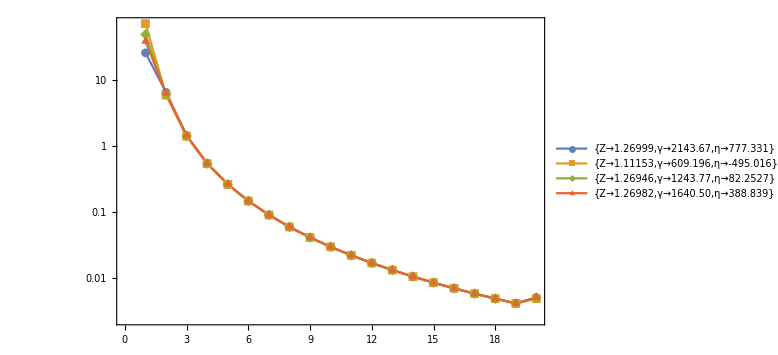

```mathematica
ListLogPlot[{%48,%45,%42,%63},Joined->True,Frame->True,PlotMarkers->Automatic,PlotLegends->{"{Z→1.26999,γ→2143.67,η→777.331}","{Z→1.11153,γ→609.196,η→-495.016}","{Z→1.26946,γ→1243.77,η→82.2527}","{Z→1.26982,γ→1640.50,η→388.839}"},ImageSize->Large]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_p4True_2.eps",%];
```

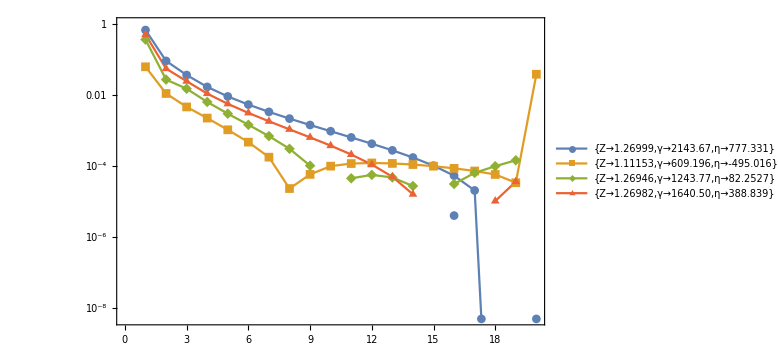

```mathematica
ListLogPlot[{%49,%46,%43,%64},Joined->True,Frame->True,PlotMarkers->Automatic,PlotLegends->{"{Z→1.26999,γ→2143.67,η→777.331}","{Z→1.11153,γ→609.196,η→-495.016}","{Z→1.26946,γ→1243.77,η→82.2527}","{Z→1.26982,γ→1640.50,η→388.839}"},ImageSize->Large]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_p4True_2_1.eps",%];
```